```mathematica
Needs["PlotLegends`"]

(* derive coeffs *)
T[x_]=4 τ x/c(c-x);
yc0[x_]=(eps x)/p^2(2 p - x/c) ;
yc1[x_]=(eps (c-x))/(1-p)^2(1+x/c-2 p);
yu0[x_,α_]=yc0[x]+T[x]/2-α x;
yu1[x_,α_]=yc1[x]+T[x]/2-α x;
yl0[x_,α_]=yc0[x]-T[x]/2-α x;
yl1[x_,α_]=yc1[x]-T[x]/2-α x;
dyu0[x_,α_]=Simplify[D[yu0[x,α],x]];
dyl0[x_,α_]=Simplify[D[yl0[x,α],x]];
dyu1[x_,α_]=Simplify[D[yu1[x,α],x]];
dyl1[x_,α_]=Simplify[D[yl1[x,α],x]];
cl[α_]=Simplify[-2/(√(Minf^2-1))1/c(Integrate[dyu0[x,α]+dyl0[x,α],{x,0,p c}]+Integrate[dyu1[x,α]+dyl1[x,α],{x,p c,c}])]
cd[α_]=Simplify[2/(√(Minf^2-1))1/c(Integrate[dyu0[x,α]^2+dyl0[x,α]^2,{x,0,p c}]+Integrate[dyu1[x,α]^2+dyl1[x,α]^2,{x,p c,c}])]
cm[α_]=Simplify[2/(√(Minf^2-1))1/c(Integrate[x(dyu0[x,α]+dyl0[x,α]),{x,0,p c}]+Integrate[x(dyu1[x,α]+dyl1[x,α]),{x,p c,c}])]
xcp[α_]=(-cm[α])/cl[α]
```

(4 α)/(√(-1+Minf^2))

-(4 (4 eps^2-(-1+p) p (3 α^2+4 τ^2)))/(3 √(-1+Minf^2) (-1+p) p)

-(2 c (4 eps+3 α))/(3 √(-1+Minf^2))

(c (4 eps+3 α))/(6 α)

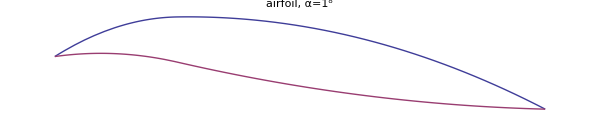

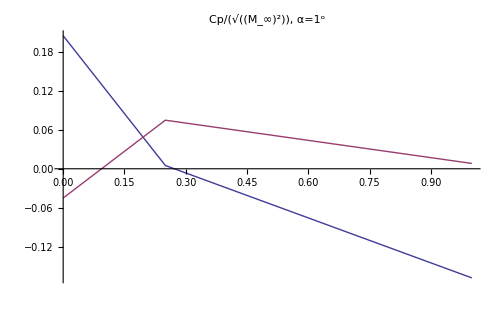

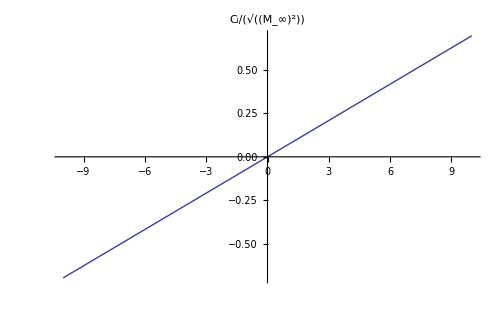

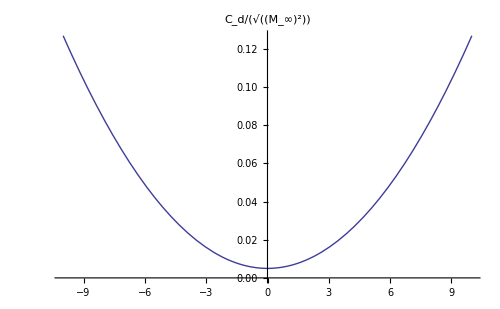

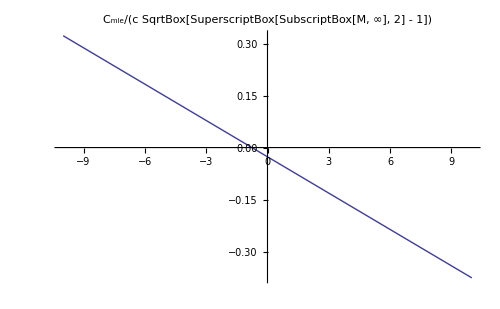

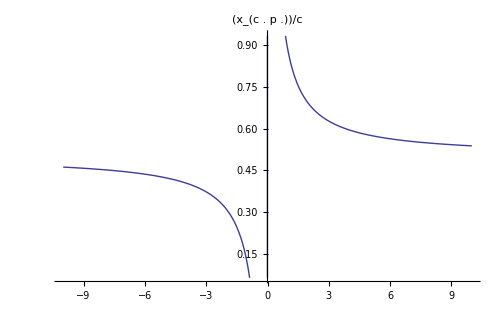

```mathematica
(* plot everything *)
subs={τ->0.02,eps->0.01,p->1/4,Minf->√2,c->1};
imsize=500;
fontsize=18;
α0=1*π/180;
Plot[{Piecewise[{{yu0[x,α0], 0 ≤ x/c ≤ p },{yu1[x,α0] ,p < x/c ≤ 1 }}]/.subs,Piecewise[{{yl0[x,α0], 0 ≤ x/c ≤ p },{yl1[x,α0] ,p < x/c ≤ 1 }}]/.subs},{x,0,1},AspectRatio->Automatic,Axes->False,ImageSize->600,PlotLabel->Style["airfoil, α=1^o",FontSize->fontsize]]
Plot[{Piecewise[{{2dyu0[x,α0], 0 ≤ x/c ≤ p },{2dyu1[x,α0] ,p < x/c ≤ 1 }}]/.subs,Piecewise[{{-2dyl0[x,α0], 0 ≤ x/c ≤ p },{-2dyl1[x,α0] ,p < x/c ≤ 1 }}]/.subs},{x,0,1},ImageSize->imsize,PlotLabel->Style["Cp/(√((M_∞)^2)), α=1^o",FontSize->fontsize]]
Plot[cl[α*π/180]/.subs,{α,-10,10},ImageSize->imsize,PlotLabel->Style["C_l/(√((M_∞)^2))",FontSize->fontsize]]
Plot[cd[α*π/180]/.subs,{α,-10,10},ImageSize->imsize,PlotLabel->Style["C_d/(√((M_∞)^2))",FontSize->fontsize]]
Plot[cm[α*π/180]/.subs,{α,-10,10},ImageSize->imsize,PlotLabel->Style["C_mle/(c SqrtBox[SuperscriptBox[SubscriptBox[M, ∞], 2] - 1])",FontSize->fontsize]]
Plot[{xcp[α π/180]/c/.subs},{α,-10,10},ImageSize->imsize,PlotLabel->Style["(x_(c . p .))/c",FontSize->fontsize]]
```